```mathematica
ClearAll["Global`*"]
```

```mathematica
y = {10.0787617156523,-9.51866467444093,9.73922587306449,11.5662681883816,9.62798489000074,-9.60265090119919,8.90114345923455,10.866328444034,10.5347883361026,8.60577222463504,-10.625227428575,-9.08615131315038,-8.99280046532217,9.43533905966944,8.92696803962787,9.642301288006,9.42066621557773,9.90838406119759,9.63911912487384,7.55585122379505,9.58069898235901,9.63228461457187,-9.99589804304319,8.61024296515084,-10.4988882191036,-8.45028703711596,9.76066425342707,-8.68129886943495,9.83763492226261,7.29698608457303,8.78881675784227,10.6057117460834,10.2807363791435,9.54352982843898,-10.9911972452721,12.2061931600758,7.76887153466896,10.7523541087606,-9.98525551020183,10.6248182699128}
```

{10.0788,-9.51866,9.73923,11.5663,9.62798,-9.60265,8.90114,10.8663,10.5348,8.60577,-10.6252,-9.08615,-8.9928,9.43534,8.92697,9.6423,9.42067,9.90838,9.63912,7.55585,9.5807,9.63228,-9.9959,8.61024,-10.4989,-8.45029,9.76066,-8.6813,9.83763,7.29699,8.78882,10.6057,10.2807,9.54353,-10.9912,12.2062,7.76887,10.7524,-9.98526,10.6248}

```mathematica
Length[y]
```

40

```mathematica
epslist = N[Range[-2,2,(2-(-2))/40]]
```

{-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.}

```mathematica
thetaRange = Range[0,1,0.2]
```

{0.,0.2,0.4,0.6,0.8,1.}

```mathematica
mu0Range = Range[-15,-5,0.05]
```

{-15.,-14.95,-14.9,-14.85,-14.8,-14.75,-14.7,-14.65,-14.6,-14.55,-14.5,-14.45,-14.4,-14.35,-14.3,-14.25,-14.2,-14.15,-14.1,-14.05,-14.,-13.95,-13.9,-13.85,-13.8,-13.75,-13.7,-13.65,-13.6,-13.55,-13.5,-13.45,-13.4,-13.35,-13.3,-13.25,-13.2,-13.15,-13.1,-13.05,-13.,-12.95,-12.9,-12.85,-12.8,-12.75,-12.7,-12.65,-12.6,-12.55,-12.5,-12.45,-12.4,-12.35,-12.3,-12.25,-12.2,-12.15,-12.1,-12.05,-12.,-11.95,-11.9,-11.85,-11.8,-11.75,-11.7,-11.65,-11.6,-11.55,-11.5,-11.45,-11.4,-11.35,-11.3,-11.25,-11.2,-11.15,-11.1,-11.05,-11.,-10.95,-10.9,-10.85,-10.8,-10.75,-10.7,-10.65,-10.6,-10.55,-10.5,-10.45,-10.4,-10.35,-10.3,-10.25,-10.2,-10.15,-10.1,-10.05,-10.,-9.95,-9.9,-9.85,-9.8,-9.75,-9.7,-9.65,-9.6,-9.55,-9.5,-9.45,-9.4,-9.35,-9.3,-9.25,-9.2,-9.15,-9.1,-9.05,-9.,-8.95,-8.9,-8.85,-8.8,-8.75,-8.7,-8.65,-8.6,-8.55,-8.5,-8.45,-8.4,-8.35,-8.3,-8.25,-8.2,-8.15,-8.1,-8.05,-8.,-7.95,-7.9,-7.85,-7.8,-7.75,-7.7,-7.65,-7.6,-7.55,-7.5,-7.45,-7.4,-7.35,-7.3,-7.25,-7.2,-7.15,-7.1,-7.05,-7.,-6.95,-6.9,-6.85,-6.8,-6.75,-6.7,-6.65,-6.6,-6.55,-6.5,-6.45,-6.4,-6.35,-6.3,-6.25,-6.2,-6.15,-6.1,-6.05,-6.,-5.95,-5.9,-5.85,-5.8,-5.75,-5.7,-5.65,-5.6,-5.55,-5.5,-5.45,-5.4,-5.35,-5.3,-5.25,-5.2,-5.15,-5.1,-5.05,-5.}

```mathematica
mu1Range = Range[5,15,5]
```

{5,10,15}

```mathematica
ptheta[theta_]:=1
```

```mathematica
pmu0[mu0_,eps_]:=PDF[NormalDistribution[-10+eps,1], mu0]
```

```mathematica
pmu1[mu1_]:=PDF[NormalDistribution[10,1],mu1]
```

```mathematica
pu[theta_, mu0_, mu1_, eps_]:=ptheta[theta]*pmu0[mu0,eps]*pmu1[mu1]
```

```mathematica
L[theta_, mu0_, mu1_, y_]:=theta *PDF[NormalDistribution[mu0,1],y]+(1-theta)*PDF[NormalDistribution[mu1,1],y]
```

```mathematica
Ltable = Table[L[theta, mu0, mu1, y[[i]]],{i, 1, Length[y]}]
```

{(ⅇ^(-1/2 (10.0788-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (10.0788-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (-9.51866-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-9.51866-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (9.73923-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.73923-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (11.5663-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (11.5663-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (9.62798-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.62798-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (-9.60265-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-9.60265-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (8.90114-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (8.90114-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (10.8663-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (10.8663-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (10.5348-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (10.5348-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (8.60577-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (8.60577-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (-10.6252-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-10.6252-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (-9.08615-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-9.08615-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (-8.9928-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-8.9928-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (9.43534-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.43534-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (8.92697-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (8.92697-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (9.6423-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.6423-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (9.42067-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.42067-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (9.90838-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.90838-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (9.63912-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.63912-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (7.55585-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (7.55585-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (9.5807-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.5807-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (9.63228-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.63228-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (-9.9959-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-9.9959-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (8.61024-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (8.61024-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (-10.4989-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-10.4989-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (-8.45029-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-8.45029-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (9.76066-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.76066-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (-8.6813-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-8.6813-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (9.83763-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.83763-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (7.29699-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (7.29699-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (8.78882-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (8.78882-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (10.6057-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (10.6057-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (10.2807-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (10.2807-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (9.54353-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.54353-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (-10.9912-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-10.9912-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (12.2062-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (12.2062-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (7.76887-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (7.76887-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (10.7524-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (10.7524-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (-9.98526-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-9.98526-mu0)^2) theta)/(√(2 π)),(ⅇ^(-1/2 (10.6248-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (10.6248-mu0)^2) theta)/(√(2 π))}

```mathematica
Ltable[[1]]
```

(ⅇ^(-1/2 (10.0788-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (10.0788-mu0)^2) theta)/(√(2 π))

```mathematica
Ltotal[theta_, mu0_, mu1_]=(Times@@Ltable)
```

((ⅇ^(-1/2 (-10.9912-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-10.9912-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (-10.6252-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-10.6252-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (-10.4989-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-10.4989-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (-9.9959-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-9.9959-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (-9.98526-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-9.98526-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (-9.60265-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-9.60265-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (-9.51866-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-9.51866-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (-9.08615-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-9.08615-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (-8.9928-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-8.9928-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (-8.6813-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-8.6813-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (-8.45029-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (-8.45029-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (7.29699-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (7.29699-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (7.55585-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (7.55585-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (7.76887-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (7.76887-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (8.60577-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (8.60577-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (8.61024-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (8.61024-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (8.78882-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (8.78882-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (8.90114-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (8.90114-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (8.92697-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (8.92697-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (9.42067-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.42067-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (9.43534-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.43534-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (9.54353-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.54353-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (9.5807-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.5807-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (9.62798-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.62798-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (9.63228-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.63228-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (9.63912-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.63912-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (9.6423-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.6423-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (9.73923-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.73923-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (9.76066-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.76066-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (9.83763-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.83763-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (9.90838-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (9.90838-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (10.0788-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (10.0788-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (10.2807-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (10.2807-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (10.5348-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (10.5348-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (10.6057-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (10.6057-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (10.6248-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (10.6248-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (10.7524-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (10.7524-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (10.8663-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (10.8663-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (11.5663-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (11.5663-mu0)^2) theta)/(√(2 π))) ((ⅇ^(-1/2 (12.2062-mu1)^2) (1-theta))/(√(2 π))+(ⅇ^(-1/2 (12.2062-mu0)^2) theta)/(√(2 π)))

```mathematica
Ltotal[theta=0.3,mu0=-13,mu1=10]
```

5.89653×10^-63

```mathematica
(*Plot3D[Ltotal[0.3,mu0, mu1], {mu0, -12,-8},{mu1, 8,12}, PlotRange->Full]*)
```

```mathematica
(*Plot3D[pu[theta=0.3,mu0,mu1,eps=0], {mu0, -12,-8},{mu1, 8,12}, PlotRange->Full]*)
```

```mathematica
plu[theta_, mu0_, mu1_, eps_]:=pu[theta, mu0, mu1, eps] *Ltotal[theta, mu0, mu1]
```

```mathematica
plu[0.3,-10,10,0]
```

1.32885×10^-37

```mathematica
(*Plot3D[plulog[0.3,mu0,mu1,eps=0], {mu0, -15,-5},{mu1, 5,15}, PlotRange->Full]*)
```

```mathematica
{time,mu0Table} = Timing[Table[NIntegrate[plu[theta, mu0, mu1,0], {theta,0,1}, {mu1,5,15}],{mu0, mu0Range}]]
```

{36.6013,{8.19031×10^-111,1.93744×10^-109,4.4476×10^-108,9.9082×10^-107,2.14208×10^-105,4.49415×10^-104,9.15019×10^-103,1.80794×10^-101,3.46665×10^-100,6.45069×10^-99,1.16486×10^-97,2.04133×10^-96,3.47154×10^-95,5.72932×10^-94,9.17604×10^-93,1.42619×10^-91,2.15116×10^-90,3.14876×10^-89,4.47276×10^-88,6.16572×10^-87,8.24828×10^-86,1.07081×10^-84,1.34907×10^-83,1.64941×10^-82,1.957×10^-81,2.25334×10^-80,2.51787×10^-79,2.7303×10^-78,2.87316×10^-77,2.93413×10^-76,2.90783×10^-75,2.79661×10^-74,2.61015×10^-73,2.36412×10^-72,2.078×10^-71,1.77252×10^-70,1.46727×10^-69,1.17869×10^-68,9.1888×10^-68,6.95168×10^-67,5.10379×10^-66,3.63636×10^-65,2.51427×10^-64,1.68705×10^-63,1.09854×10^-62,6.94181×10^-62,4.25699×10^-61,2.5334×10^-60,1.4631×10^-59,8.20008×10^-59,4.45997×10^-58,2.35406×10^-57,1.2058×10^-56,5.99379×10^-56,2.89135×10^-55,1.35354×10^-54,6.1491×10^-54,2.71097×10^-53,1.15987×10^-52,4.81573×10^-52,1.94039×10^-51,7.58726×10^-51,2.87908×10^-50,1.06021×10^-49,3.78881×10^-49,1.31397×10^-48,4.42219×10^-48,1.44431×10^-47,4.5778×10^-47,1.40807×10^-46,4.20301×10^-46,1.2175×10^-45,3.42255×10^-45,9.33685×10^-45,2.47185×10^-44,6.35061×10^-44,1.58336×10^-43,3.83103×10^-43,8.99544×10^-43,2.04975×10^-42,4.53263×10^-42,9.7268×10^-42,2.02564×10^-41,4.09378×10^-41,8.02894×10^-41,1.52814×10^-40,2.82253×10^-40,5.05925×10^-40,8.80045×10^-40,1.48558×10^-39,2.43364×10^-39,3.8689×10^-39,5.96885×10^-39,8.93645×10^-39,1.29841×10^-38,1.83074×10^-38,2.50504×10^-38,3.3264×10^-38,4.28651×10^-38,5.3605×10^-38,6.50546×10^-38,7.66163×10^-38,8.75661×10^-38,9.7123×10^-38,1.04539×10^-37,1.09196×10^-37,1.1069×10^-37,1.08887×10^-37,1.03949×10^-37,9.63014×10^-38,8.65798×10^-38,7.55391×10^-38,6.39585×10^-38,5.25528×10^-38,4.19049×10^-38,3.24268×10^-38,2.43509×10^-38,1.77459×10^-38,1.25502×10^-38,8.61343×10^-39,5.73683×10^-39,3.70799×10^-39,2.32582×10^-39,1.41575×10^-39,8.36309×10^-40,4.79422×10^-40,2.66711×10^-40,1.43991×10^-40,7.54397×10^-41,3.83563×10^-41,1.89253×10^-41,9.06197×10^-42,4.21087×10^-42,1.89886×10^-42,8.3097×10^-43,3.52897×10^-43,1.4544×10^-43,5.81686×10^-44,2.25769×10^-44,8.5038×10^-45,3.10837×10^-45,1.10261×10^-45,3.79563×10^-46,1.26799×10^-46,4.11074×10^-47,1.29329×10^-47,3.94858×10^-48,1.16993×10^-48,3.36393×10^-49,9.38656×10^-50,2.54178×10^-50,6.67943×10^-51,1.70338×10^-51,4.21557×10^-52,1.01245×10^-52,2.35971×10^-53,5.33723×10^-54,1.17151×10^-54,2.49543×10^-55,5.15842×10^-56,1.03481×10^-56,2.01452×10^-57,3.8059×10^-58,6.97771×10^-59,1.24148×10^-59,2.14357×10^-60,3.59176×10^-61,5.84048×10^-62,9.21637×10^-63,1.41138×10^-63,2.09748×10^-64,3.02498×10^-65,4.23369×10^-66,5.75024×10^-67,7.57923×10^-68,9.69471×10^-69,1.20342×10^-69,1.44967×10^-70,1.69469×10^-71,1.92259×10^-72,2.11666×10^-73,2.26146×10^-74,2.34475×10^-75,2.35926×10^-76,2.3037×10^-77,2.18297×10^-78,2.00743×10^-79,1.79145×10^-80,1.55146×10^-81,1.3039×10^-82,1.06346×10^-83,8.41727×10^-85,6.46534×10^-86,4.81928×10^-87,3.48613×10^-88,2.44724×10^-89,1.66718×10^-90,1.10219×10^-91,7.07137×10^-93,4.40273×10^-94,2.66018×10^-95}}

```mathematica
mu0norm = Total[mu0Table]
mu0Table = mu0Table/mu0norm
mu0TrueCDF = Table[Function[upto,Sum[mu0Table[[i]], {i, 1,upto}]][i], {i,1, Length[mu0Table]}]
```

1.60196×10^-36

{5.11269×10^-75,1.20942×10^-73,2.77635×10^-72,6.18506×10^-71,1.33716×10^-69,2.80541×10^-68,5.71188×10^-67,1.12858×10^-65,2.16401×10^-64,4.02675×10^-63,7.27148×10^-62,1.27427×10^-60,2.16706×10^-59,3.57645×10^-58,5.72802×10^-57,8.90283×10^-56,1.34283×10^-54,1.96557×10^-53,2.79206×10^-52,3.84887×10^-51,5.14888×10^-50,6.68441×10^-49,8.4214×10^-48,1.02962×10^-46,1.22163×10^-45,1.40662×10^-44,1.57175×10^-43,1.70435×10^-42,1.79353×10^-41,1.83159×10^-40,1.81518×10^-39,1.74575×10^-38,1.62935×10^-37,1.47577×10^-36,1.29716×10^-35,1.10647×10^-34,9.15922×10^-34,7.35779×10^-33,5.73598×10^-32,4.3395×10^-31,3.18597×10^-30,2.26995×10^-29,1.5695×10^-28,1.05312×10^-27,6.85746×10^-27,4.33333×10^-26,2.65737×10^-25,1.58144×10^-24,9.13322×10^-24,5.11879×10^-23,2.78408×10^-22,1.46949×10^-21,7.52702×10^-21,3.74154×10^-20,1.80489×10^-19,8.44928×10^-19,3.83849×10^-18,1.69228×10^-17,7.2403×10^-17,3.00616×10^-16,1.21126×10^-15,4.73625×10^-15,1.79722×10^-14,6.61823×10^-14,2.36512×10^-13,8.20227×10^-13,2.76049×10^-12,9.01594×10^-12,2.85763×10^-11,8.78966×10^-11,2.62367×10^-10,7.60009×10^-10,2.13648×10^-9,5.8284×10^-9,1.54302×10^-8,3.96428×10^-8,9.88392×10^-8,2.39147×10^-7,5.61528×10^-7,1.27953×10^-6,2.82943×10^-6,6.07183×10^-6,0.0000126448,0.0000255549,0.0000501196,0.0000953921,0.000176193,0.000315817,0.000549356,0.00092735,0.00151916,0.00241511,0.00372597,0.00557846,0.00810512,0.0114282,0.0156374,0.0207646,0.026758,0.0334622,0.0406094,0.0478267,0.054662,0.0606277,0.0652572,0.0681643,0.0690965,0.0679715,0.0648886,0.0601148,0.0540463,0.0471543,0.0399252,0.0328054,0.0261586,0.020242,0.0152007,0.0110776,0.00783431,0.00537682,0.00358114,0.00231466,0.00145186,0.000883762,0.000522054,0.000299273,0.000166491,0.0000898844,0.0000470922,0.0000239434,0.0000118139,5.65681×10^-6,2.62858×10^-6,1.18534×10^-6,5.18722×10^-7,2.20291×10^-7,9.07887×10^-8,3.6311×10^-8,1.40934×10^-8,5.30838×10^-9,1.94036×10^-9,6.8829×10^-10,2.36937×10^-10,7.91527×10^-11,2.56608×10^-11,8.07317×10^-12,2.46485×10^-12,7.30311×10^-13,2.09989×10^-13,5.85943×10^-14,1.58667×10^-14,4.16954×10^-15,1.06331×10^-15,2.63151×10^-16,6.32006×10^-17,1.47302×10^-17,3.3317×10^-18,7.31298×10^-19,1.55774×10^-19,3.22007×10^-20,6.45964×10^-21,1.25754×10^-21,2.37578×10^-22,4.35574×10^-23,7.74978×10^-24,1.3381×10^-24,2.24211×10^-25,3.64584×10^-26,5.7532×10^-27,8.81033×10^-28,1.30932×10^-28,1.8883×10^-29,2.64282×10^-30,3.58951×10^-31,4.73123×10^-32,6.05179×10^-33,7.51216×10^-34,9.04935×10^-35,1.05789×10^-35,1.20015×10^-36,1.3213×10^-37,1.41168×10^-38,1.46368×10^-39,1.47274×10^-40,1.43805×10^-41,1.36269×10^-42,1.25311×10^-43,1.11829×10^-44,9.68475×10^-46,8.13944×10^-47,6.63853×10^-48,5.25437×10^-49,4.0359×10^-50,3.00837×10^-51,2.17617×10^-52,1.52766×10^-53,1.04071×10^-54,6.88028×10^-56,4.41421×10^-57,2.74834×10^-58,1.66058×10^-59}

{5.11269×10^-75,1.26055×10^-73,2.90241×10^-72,6.4753×10^-71,1.40192×10^-69,2.9456×10^-68,6.00644×10^-67,1.18865×10^-65,2.28287×10^-64,4.25504×10^-63,7.69698×10^-62,1.35124×10^-60,2.30219×10^-59,3.80667×10^-58,6.10869×10^-57,9.5137×10^-56,1.43797×10^-54,2.10937×10^-53,3.003×10^-52,4.14917×10^-51,5.56379×10^-50,7.24079×10^-49,9.14548×10^-48,1.12108×10^-46,1.33374×10^-45,1.53999×10^-44,1.72574×10^-43,1.87693×10^-42,1.98122×10^-41,2.02971×10^-40,2.01815×10^-39,1.94756×10^-38,1.8241×10^-37,1.65818×10^-36,1.46298×10^-35,1.25277×10^-34,1.0412×10^-33,8.39899×10^-33,6.57588×10^-32,4.99708×10^-31,3.68568×10^-30,2.63851×10^-29,1.83335×10^-28,1.23645×10^-27,8.09392×10^-27,5.14272×10^-26,3.17164×10^-25,1.8986×10^-24,1.10318×10^-23,6.22197×10^-23,3.40627×10^-22,1.81012×10^-21,9.33714×10^-21,4.67526×10^-20,2.27241×10^-19,1.07217×10^-18,4.91066×10^-18,2.18335×10^-17,9.42365×10^-17,3.94852×10^-16,1.60611×10^-15,6.34236×10^-15,2.43146×10^-14,9.04969×10^-14,3.27008×10^-13,1.14724×10^-12,3.90773×10^-12,1.29237×10^-11,4.15×10^-11,1.29397×10^-10,3.91764×10^-10,1.15177×10^-9,3.28825×10^-9,9.11665×10^-9,2.45468×10^-8,6.41897×10^-8,1.63029×10^-7,4.02176×10^-7,9.63704×10^-7,2.24323×10^-6,5.07266×10^-6,0.0000111445,0.0000237893,0.0000493441,0.0000994637,0.000194856,0.000371049,0.000686866,0.00123622,0.00216357,0.00368274,0.00609784,0.00982382,0.0154023,0.0235074,0.0349356,0.0505729,0.0713375,0.0980955,0.131558,0.172167,0.219994,0.274656,0.335284,0.400541,0.468705,0.537801,0.605773,0.670662,0.730776,0.784823,0.831977,0.871902,0.904708,0.930866,0.951108,0.966309,0.977387,0.985221,0.990598,0.994179,0.996493,0.997945,0.998829,0.999351,0.99965,0.999817,0.999907,0.999954,0.999978,0.99999,0.999995,0.999998,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
exp = Total[mu0Range* mu0Table]
```

-9.70236

```mathematica
NumberForm[exp,16]
```

-9.70235997557161

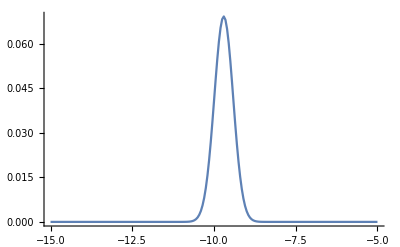

```mathematica
ListLinePlot[Transpose[{mu0Range,mu0Table}],PlotRange->{Automatic,Full}]
```

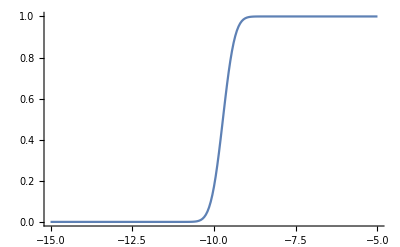

```mathematica
ListLinePlot[Transpose[{mu0Range,mu0TrueCDF}],PlotRange->{Automatic,Full}]
```

```mathematica
matrix = Table[0,{r,Length[mu0Range]},{c, Length[epslist]}]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
For[i = 1, i <= Length[epslist], i++,
 e = epslist[[i]];
mu0TableEps = Table[NIntegrate[plu[theta, mu0, mu1,e], {theta,0,1}, {mu1,5,15}],{mu0, mu0Range}];
 mu0normEps = Total[mu0TableEps];
mu0TableEps = mu0TableEps/mu0normEps;
mu0CDFEps = Table[Function[upto,Sum[mu0TableEps[[i]], {i, 1,upto}]][i], {i,1, Length[mu0TableEps]}];
matrix[[All,i]] = mu0CDFEps;
 ]
```

```mathematica
KS = Table[Max[Abs[matrix[[All, i]] - mu0TrueCDF]],{i,1,Length[epslist]}]
```

{0.227295,0.216311,0.205232,0.194067,0.182825,0.171514,0.160143,0.148723,0.137261,0.125903,0.114661,0.10335,0.0919791,0.0805583,0.0690965,0.0576033,0.0460881,0.0345605,0.0230302,0.0115069,0.,0.0114933,0.0230085,0.034536,0.0460663,0.0575897,0.0690965,0.0805773,0.0920225,0.103423,0.114769,0.126051,0.137261,0.148549,0.159994,0.171394,0.18274,0.194022,0.205232,0.216361,0.227399}

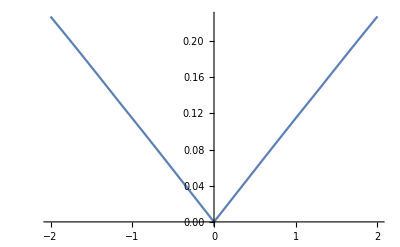

```mathematica
ListLinePlot[Transpose[{epslist,KS}],PlotRange->{Automatic,Full}]
```

```mathematica
Export[NotebookDirectory[]<>"normal_mixture_mu[0]_1.csv",{epslist,mu0Range,matrix, KS}]
```

/home/ez/sense/benchmarks/stan_bench/normal_mixture/normal_mixture_mu[0]_1.csv

```mathematica
AQUAmu0Range = {-10.80000019,-10.79266644,-10.78533363,-10.77799988,-10.77066708,-10.76333332,-10.75600052,-10.74866676,-10.74133396,-10.73400021,-10.72666645,-10.71933365,-10.71199989,-10.70466709,-10.69733334,-10.69000053,-10.68266678,-10.67533398,-10.66800022,-10.66066647,-10.65333366,-10.64599991,-10.63866711,-10.63133335,-10.62400055,-10.61666679,-10.60933399,-10.60200024,-10.59466648,-10.58733368,-10.57999992,-10.57266712,-10.56533337,-10.55800056,-10.55066681,-10.54333401,-10.53600025,-10.52866650,-10.52133369,-10.51399994,-10.50666714,-10.49933338,-10.49200058,-10.48466682,-10.47733402,-10.47000027,-10.46266651,-10.45533371,-10.44799995,-10.44066715,-10.43333340,-10.42600060,-10.41866684,-10.41133308,-10.40400028,-10.39666653,-10.38933372,-10.38199997,-10.37466717,-10.36733341,-10.36000061,-10.35266685,-10.34533310,-10.33800030,-10.33066654,-10.32333374,-10.31599998,-10.30866718,-10.30133343,-10.29400063,-10.28666687,-10.27933311,-10.27200031,-10.26466656,-10.25733376,-10.25000000,-10.24266720,-10.23533344,-10.22800064,-10.22066689,-10.21333313,-10.20600033,-10.19866657,-10.19133377,-10.18400002,-10.17666721,-10.16933346,-10.16200066,-10.15466690,-10.14733315,-10.14000034,-10.13266659,-10.12533379,-10.11800003,-10.11066723,-10.10333347,-10.09600067,-10.08866692,-10.08133316,-10.07400036,-10.06666660,-10.05933380,-10.05200005,-10.04466724,-10.03733349,-10.03000069,-10.02266693,-10.01533318,-10.00800037,-10.00066662,-9.99333382,-9.98600006,-9.97866726,-9.97133350,-9.96400070,-9.95666695,-9.94933319,-9.94200039,-9.93466663,-9.92733383,-9.92000008,-9.91266727,-9.90533352,-9.89800072,-9.89066696,-9.88333321,-9.87600040,-9.86866665,-9.86133385,-9.85400009,-9.84666729,-9.83933353,-9.83200073,-9.82466698,-9.81733322,-9.81000042,-9.80266666,-9.79533386,-9.78800011,-9.78066730,-9.77333355,-9.76600075,-9.75866699,-9.75133324,-9.74400043,-9.73666668,-9.72933388,-9.72200012,-9.71466732,-9.70733356,-9.70000076,-9.69266701,-9.68533325,-9.67800045,-9.67066669,-9.66333389,-9.65600014,-9.64866734,-9.64133358,-9.63399982,-9.62666702,-9.61933327,-9.61200047,-9.60466671,-9.59733391,-9.59000015,-9.58266735,-9.57533360,-9.56799984,-9.56066704,-9.55333328,-9.54600048,-9.53866673,-9.53133392,-9.52400017,-9.51666737,-9.50933361,-9.50199986,-9.49466705,-9.48733330,-9.48000050,-9.47266674,-9.46533394,-9.45800018,-9.45066738,-9.44333363,-9.43599987,-9.42866707,-9.42133331,-9.41400051,-9.40666676,-9.39933395,-9.39200020,-9.38466740,-9.37733364,-9.36999989,-9.36266708,-9.35533333,-9.34800053,-9.34066677,-9.33333397,-9.32600021,-9.31866741,-9.31133366,-9.30399990,-9.29666710,-9.28933334,-9.28200054,-9.27466679,-9.26733398,-9.26000023,-9.25266743,-9.24533367,-9.23799992,-9.23066711,-9.22333336,-9.21600056,-9.20866680,-9.20133400,-9.19400024,-9.18666744,-9.17933369,-9.17199993,-9.16466713,-9.15733337,-9.15000057,-9.14266682,-9.13533401,-9.12800026,-9.12066746,-9.11333370,-9.10599995,-9.09866714,-9.09133339,-9.08400059,-9.07666683,-9.06933403,-9.06200027,-9.05466747,-9.04733372,-9.03999996,-9.03266716,-9.02533340,-9.01800060,-9.01066685,-9.00333405,-8.99600029,-8.98866749,-8.98133373,-8.97399998,-8.96666718,-8.95933342,-8.95200062,-8.94466686,-8.93733406,-8.93000031,-8.92266655,-8.91533375,-8.90799999,-8.90066719,-8.89333344,-8.88600063,-8.87866688,-8.87133408,-8.86400032,-8.85666656,-8.84933376,-8.84200001,-8.83466721,-8.82733345,-8.82000065,-8.81266689,-8.80533409,-8.79800034,-8.79066658,-8.78333378,-8.77600002,-8.76866722,-8.76133347,-8.75400066,-8.74666691,-8.73933411,-8.73200035,-8.72466660,-8.71733379,-8.71000004,-8.70266724,-8.69533348,-8.68800068,-8.68066692,-8.67333412,-8.66600037,-8.65866661,-8.65133381,-8.64400005,-8.63666725,-8.62933350,-8.62200069,-8.61466694,-8.60733414,-8.60000038}
```

{-10.8,-10.7927,-10.7853,-10.778,-10.7707,-10.7633,-10.756,-10.7487,-10.7413,-10.734,-10.7267,-10.7193,-10.712,-10.7047,-10.6973,-10.69,-10.6827,-10.6753,-10.668,-10.6607,-10.6533,-10.646,-10.6387,-10.6313,-10.624,-10.6167,-10.6093,-10.602,-10.5947,-10.5873,-10.58,-10.5727,-10.5653,-10.558,-10.5507,-10.5433,-10.536,-10.5287,-10.5213,-10.514,-10.5067,-10.4993,-10.492,-10.4847,-10.4773,-10.47,-10.4627,-10.4553,-10.448,-10.4407,-10.4333,-10.426,-10.4187,-10.4113,-10.404,-10.3967,-10.3893,-10.382,-10.3747,-10.3673,-10.36,-10.3527,-10.3453,-10.338,-10.3307,-10.3233,-10.316,-10.3087,-10.3013,-10.294,-10.2867,-10.2793,-10.272,-10.2647,-10.2573,-10.25,-10.2427,-10.2353,-10.228,-10.2207,-10.2133,-10.206,-10.1987,-10.1913,-10.184,-10.1767,-10.1693,-10.162,-10.1547,-10.1473,-10.14,-10.1327,-10.1253,-10.118,-10.1107,-10.1033,-10.096,-10.0887,-10.0813,-10.074,-10.0667,-10.0593,-10.052,-10.0447,-10.0373,-10.03,-10.0227,-10.0153,-10.008,-10.0007,-9.99333,-9.986,-9.97867,-9.97133,-9.964,-9.95667,-9.94933,-9.942,-9.93467,-9.92733,-9.92,-9.91267,-9.90533,-9.898,-9.89067,-9.88333,-9.876,-9.86867,-9.86133,-9.854,-9.84667,-9.83933,-9.832,-9.82467,-9.81733,-9.81,-9.80267,-9.79533,-9.788,-9.78067,-9.77333,-9.766,-9.75867,-9.75133,-9.744,-9.73667,-9.72933,-9.722,-9.71467,-9.70733,-9.7,-9.69267,-9.68533,-9.678,-9.67067,-9.66333,-9.656,-9.64867,-9.64133,-9.634,-9.62667,-9.61933,-9.612,-9.60467,-9.59733,-9.59,-9.58267,-9.57533,-9.568,-9.56067,-9.55333,-9.546,-9.53867,-9.53133,-9.524,-9.51667,-9.50933,-9.502,-9.49467,-9.48733,-9.48,-9.47267,-9.46533,-9.458,-9.45067,-9.44333,-9.436,-9.42867,-9.42133,-9.414,-9.40667,-9.39933,-9.392,-9.38467,-9.37733,-9.37,-9.36267,-9.35533,-9.348,-9.34067,-9.33333,-9.326,-9.31867,-9.31133,-9.304,-9.29667,-9.28933,-9.282,-9.27467,-9.26733,-9.26,-9.25267,-9.24533,-9.238,-9.23067,-9.22333,-9.216,-9.20867,-9.20133,-9.194,-9.18667,-9.17933,-9.172,-9.16467,-9.15733,-9.15,-9.14267,-9.13533,-9.128,-9.12067,-9.11333,-9.106,-9.09867,-9.09133,-9.084,-9.07667,-9.06933,-9.062,-9.05467,-9.04733,-9.04,-9.03267,-9.02533,-9.018,-9.01067,-9.00333,-8.996,-8.98867,-8.98133,-8.974,-8.96667,-8.95933,-8.952,-8.94467,-8.93733,-8.93,-8.92267,-8.91533,-8.908,-8.90067,-8.89333,-8.886,-8.87867,-8.87133,-8.864,-8.85667,-8.84933,-8.842,-8.83467,-8.82733,-8.82,-8.81267,-8.80533,-8.798,-8.79067,-8.78333,-8.776,-8.76867,-8.76133,-8.754,-8.74667,-8.73933,-8.732,-8.72467,-8.71733,-8.71,-8.70267,-8.69533,-8.688,-8.68067,-8.67333,-8.666,-8.65867,-8.65133,-8.644,-8.63667,-8.62933,-8.622,-8.61467,-8.60733,-8.6}

```mathematica
AQUAmu0Table = {0.00000735,0.00000809,0.00000891,0.00000979,0.00001076,0.00001182,0.00001297,0.00001423,0.00001560,0.00001708,0.00001870,0.00002046,0.00002237,0.00002444,0.00002668,0.00002911,0.00003175,0.00003460,0.00003768,0.00004101,0.00004460,0.00004848,0.00005266,0.00005716,0.00006201,0.00006723,0.00007284,0.00007886,0.00008533,0.00009227,0.00009972,0.00010769,0.00011622,0.00012535,0.00013511,0.00014553,0.00015666,0.00016853,0.00018119,0.00019466,0.00020901,0.00022427,0.00024048,0.00025770,0.00027598,0.00029536,0.00031590,0.00033765,0.00036067,0.00038500,0.00041071,0.00043786,0.00046650,0.00049669,0.00052850,0.00056198,0.00059719,0.00063420,0.00067307,0.00071387,0.00075664,0.00080146,0.00084839,0.00089749,0.00094882,0.00100243,0.00105839,0.00111675,0.00117758,0.00124091,0.00130681,0.00137532,0.00144648,0.00152036,0.00159696,0.00167635,0.00175854,0.00184359,0.00193148,0.00202228,0.00211597,0.00221257,0.00231209,0.00241453,0.00251989,0.00262813,0.00273927,0.00285325,0.00297008,0.00308969,0.00321203,0.00333707,0.00346473,0.00359497,0.00372769,0.00386282,0.00400025,0.00413992,0.00428171,0.00442547,0.00457113,0.00471851,0.00486753,0.00501800,0.00516979,0.00532273,0.00547667,0.00563143,0.00578680,0.00594265,0.00609874,0.00625491,0.00641091,0.00656659,0.00672170,0.00687604,0.00702940,0.00718152,0.00733222,0.00748123,0.00762837,0.00777335,0.00791600,0.00805606,0.00819333,0.00832754,0.00845848,0.00858596,0.00870973,0.00882959,0.00894530,0.00905671,0.00916358,0.00926573,0.00936298,0.00945513,0.00954204,0.00962353,0.00969947,0.00976969,0.00983407,0.00989248,0.00994483,0.00999102,0.01003092,0.01006450,0.01009168,0.01011239,0.01012662,0.01013433,0.01013549,0.01013012,0.01011822,0.01009981,0.01007492,0.01004362,0.01000596,0.00996202,0.00991186,0.00985557,0.00979332,0.00972516,0.00965126,0.00957172,0.00948674,0.00939642,0.00930097,0.00920055,0.00909533,0.00898553,0.00887132,0.00875292,0.00863051,0.00850435,0.00837461,0.00824154,0.00810533,0.00796623,0.00782449,0.00768030,0.00753391,0.00738553,0.00723542,0.00708377,0.00693085,0.00677682,0.00662196,0.00646647,0.00631054,0.00615441,0.00599826,0.00584232,0.00568674,0.00553176,0.00537751,0.00522418,0.00507197,0.00492100,0.00477146,0.00462347,0.00447719,0.00433273,0.00419024,0.00404980,0.00391155,0.00377559,0.00364199,0.00351087,0.00338227,0.00325630,0.00313298,0.00301240,0.00289458,0.00277957,0.00266742,0.00255813,0.00245176,0.00234827,0.00224771,0.00215007,0.00205535,0.00196352,0.00187458,0.00178853,0.00170532,0.00162494,0.00154734,0.00147251,0.00140038,0.00133093,0.00126411,0.00119986,0.00113815,0.00107892,0.00102211,0.00096766,0.00091553,0.00086564,0.00081795,0.00077238,0.00072888,0.00068739,0.00064784,0.00061017,0.00057433,0.00054024,0.00050784,0.00047708,0.00044790,0.00042022,0.00039401,0.00036919,0.00034571,0.00032351,0.00030255,0.00028276,0.00026409,0.00024650,0.00022993,0.00021434,0.00019967,0.00018589,0.00017295,0.00016081,0.00014942,0.00013875,0.00012875,0.00011940,0.00011066,0.00010249,0.00009487,0.00008775,0.00008112,0.00007494,0.00006918,0.00006383,0.00005885,0.00005422,0.00004993,0.00004595,0.00004226,0.00003883,0.00003567,0.00003274,0.00003003,0.00002753,0.00002522,0.00002309,0.00002112,0.00001931,0.00001765,0.00001611,0.00001470,0.00001341,0.00001222,0.00001113,0.00001013,0.00000921,0.00000838,0.00000761,0.00000691}
```

{7.35×10^-6,8.09×10^-6,8.91×10^-6,9.79×10^-6,0.00001076,0.00001182,0.00001297,0.00001423,0.0000156,0.00001708,0.0000187,0.00002046,0.00002237,0.00002444,0.00002668,0.00002911,0.00003175,0.0000346,0.00003768,0.00004101,0.0000446,0.00004848,0.00005266,0.00005716,0.00006201,0.00006723,0.00007284,0.00007886,0.00008533,0.00009227,0.00009972,0.00010769,0.00011622,0.00012535,0.00013511,0.00014553,0.00015666,0.00016853,0.00018119,0.00019466,0.00020901,0.00022427,0.00024048,0.0002577,0.00027598,0.00029536,0.0003159,0.00033765,0.00036067,0.000385,0.00041071,0.00043786,0.0004665,0.00049669,0.0005285,0.00056198,0.00059719,0.0006342,0.00067307,0.00071387,0.00075664,0.00080146,0.00084839,0.00089749,0.00094882,0.00100243,0.00105839,0.00111675,0.00117758,0.00124091,0.00130681,0.00137532,0.00144648,0.00152036,0.00159696,0.00167635,0.00175854,0.00184359,0.00193148,0.00202228,0.00211597,0.00221257,0.00231209,0.00241453,0.00251989,0.00262813,0.00273927,0.00285325,0.00297008,0.00308969,0.00321203,0.00333707,0.00346473,0.00359497,0.00372769,0.00386282,0.00400025,0.00413992,0.00428171,0.00442547,0.00457113,0.00471851,0.00486753,0.005018,0.00516979,0.00532273,0.00547667,0.00563143,0.0057868,0.00594265,0.00609874,0.00625491,0.00641091,0.00656659,0.0067217,0.00687604,0.0070294,0.00718152,0.00733222,0.00748123,0.00762837,0.00777335,0.007916,0.00805606,0.00819333,0.00832754,0.00845848,0.00858596,0.00870973,0.00882959,0.0089453,0.00905671,0.00916358,0.00926573,0.00936298,0.00945513,0.00954204,0.00962353,0.00969947,0.00976969,0.00983407,0.00989248,0.00994483,0.00999102,0.0100309,0.0100645,0.0100917,0.0101124,0.0101266,0.0101343,0.0101355,0.0101301,0.0101182,0.0100998,0.0100749,0.0100436,0.010006,0.00996202,0.00991186,0.00985557,0.00979332,0.00972516,0.00965126,0.00957172,0.00948674,0.00939642,0.00930097,0.00920055,0.00909533,0.00898553,0.00887132,0.00875292,0.00863051,0.00850435,0.00837461,0.00824154,0.00810533,0.00796623,0.00782449,0.0076803,0.00753391,0.00738553,0.00723542,0.00708377,0.00693085,0.00677682,0.00662196,0.00646647,0.00631054,0.00615441,0.00599826,0.00584232,0.00568674,0.00553176,0.00537751,0.00522418,0.00507197,0.004921,0.00477146,0.00462347,0.00447719,0.00433273,0.00419024,0.0040498,0.00391155,0.00377559,0.00364199,0.00351087,0.00338227,0.0032563,0.00313298,0.0030124,0.00289458,0.00277957,0.00266742,0.00255813,0.00245176,0.00234827,0.00224771,0.00215007,0.00205535,0.00196352,0.00187458,0.00178853,0.00170532,0.00162494,0.00154734,0.00147251,0.00140038,0.00133093,0.00126411,0.00119986,0.00113815,0.00107892,0.00102211,0.00096766,0.00091553,0.00086564,0.00081795,0.00077238,0.00072888,0.00068739,0.00064784,0.00061017,0.00057433,0.00054024,0.00050784,0.00047708,0.0004479,0.00042022,0.00039401,0.00036919,0.00034571,0.00032351,0.00030255,0.00028276,0.00026409,0.0002465,0.00022993,0.00021434,0.00019967,0.00018589,0.00017295,0.00016081,0.00014942,0.00013875,0.00012875,0.0001194,0.00011066,0.00010249,0.00009487,0.00008775,0.00008112,0.00007494,0.00006918,0.00006383,0.00005885,0.00005422,0.00004993,0.00004595,0.00004226,0.00003883,0.00003567,0.00003274,0.00003003,0.00002753,0.00002522,0.00002309,0.00002112,0.00001931,0.00001765,0.00001611,0.0000147,0.00001341,0.00001222,0.00001113,0.00001013,9.21×10^-6,8.38×10^-6,7.61×10^-6,6.91×10^-6}

```mathematica
Total[mu0Table * mu0Range]
```

-9.70236

```mathematica
Total[AQUAmu0Table * AQUAmu0Range]
```

-9.70236

```mathematica
AQUACDF = Table[Function[upto,Sum[AQUAmu0Table[[i]], {i, 1,upto}]][i], {i,1, Length[AQUAmu0Range]}]
```

{7.35×10^-6,0.00001544,0.00002435,0.00003414,0.0000449,0.00005672,0.00006969,0.00008392,0.00009952,0.0001166,0.0001353,0.00015576,0.00017813,0.00020257,0.00022925,0.00025836,0.00029011,0.00032471,0.00036239,0.0004034,0.000448,0.00049648,0.00054914,0.0006063,0.00066831,0.00073554,0.00080838,0.00088724,0.00097257,0.00106484,0.00116456,0.00127225,0.00138847,0.00151382,0.00164893,0.00179446,0.00195112,0.00211965,0.00230084,0.0024955,0.00270451,0.00292878,0.00316926,0.00342696,0.00370294,0.0039983,0.0043142,0.00465185,0.00501252,0.00539752,0.00580823,0.00624609,0.00671259,0.00720928,0.00773778,0.00829976,0.00889695,0.00953115,0.0102042,0.0109181,0.0116747,0.0124762,0.0133246,0.0142221,0.0151709,0.0161733,0.0172317,0.0183485,0.019526,0.020767,0.0220738,0.0234491,0.0248956,0.0264159,0.0280129,0.0296892,0.0314478,0.0332914,0.0352228,0.0372451,0.0393611,0.0415737,0.0438858,0.0463003,0.0488202,0.0514483,0.0541876,0.0570408,0.0600109,0.0631006,0.0663126,0.0696497,0.0731144,0.0767094,0.0804371,0.0842999,0.0883002,0.0924401,0.0967218,0.101147,0.105718,0.110437,0.115304,0.120322,0.125492,0.130815,0.136292,0.141923,0.14771,0.153652,0.159751,0.166006,0.172417,0.178984,0.185705,0.192581,0.199611,0.206792,0.214125,0.221606,0.229234,0.237007,0.244923,0.25298,0.261173,0.2695,0.277959,0.286545,0.295255,0.304084,0.313029,0.322086,0.33125,0.340515,0.349878,0.359334,0.368876,0.378499,0.388199,0.397968,0.407802,0.417695,0.42764,0.437631,0.447662,0.457726,0.467818,0.47793,0.488057,0.498191,0.508327,0.518457,0.528575,0.538675,0.54875,0.558793,0.568799,0.578761,0.588673,0.598529,0.608322,0.618047,0.627698,0.63727,0.646757,0.656153,0.665454,0.674655,0.68375,0.692736,0.701607,0.71036,0.718991,0.727495,0.735869,0.744111,0.752216,0.760183,0.768007,0.775687,0.783221,0.790607,0.797842,0.804926,0.811857,0.818634,0.825256,0.831722,0.838033,0.844187,0.850185,0.856028,0.861714,0.867246,0.872624,0.877848,0.88292,0.887841,0.892612,0.897236,0.901713,0.906046,0.910236,0.914286,0.918197,0.921973,0.925615,0.929126,0.932508,0.935764,0.938897,0.94191,0.944804,0.947584,0.950251,0.952809,0.955261,0.957609,0.959857,0.962007,0.964062,0.966026,0.967901,0.969689,0.971394,0.973019,0.974567,0.976039,0.97744,0.978771,0.980035,0.981234,0.982373,0.983452,0.984474,0.985441,0.986357,0.987223,0.98804,0.988813,0.989542,0.990229,0.990877,0.991487,0.992061,0.992602,0.99311,0.993587,0.994035,0.994455,0.994849,0.995218,0.995564,0.995887,0.99619,0.996472,0.996737,0.996983,0.997213,0.997427,0.997627,0.997813,0.997986,0.998147,0.998296,0.998435,0.998564,0.998683,0.998794,0.998896,0.998991,0.999079,0.99916,0.999235,0.999304,0.999368,0.999427,0.999481,0.999531,0.999577,0.999619,0.999658,0.999694,0.999726,0.999756,0.999784,0.999809,0.999832,0.999853,0.999873,0.99989,0.999906,0.999921,0.999934,0.999947,0.999958,0.999968,0.999977,0.999985,0.999993,1.}

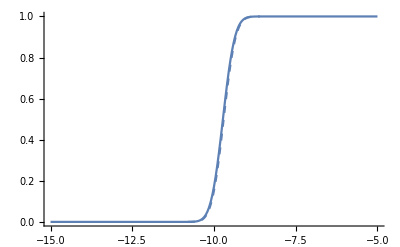

```mathematica
Show[ListLinePlot[Transpose[{mu0Range,mu0TrueCDF}],PlotRange->{Automatic,Full}],ListLinePlot[Transpose[{AQUAmu0Range,AQUACDF}],PlotRange->{Automatic,Full}, PlotStyle->Dashed]]
```